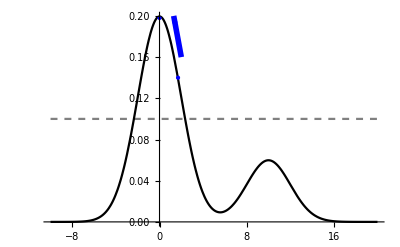

```mathematica
plot1=Plot[{0.1,PDF[NormalDistribution[0,2],x]+0.3PDF[NormalDistribution[10,2],x]},{x,-10,20},PlotStyle->{{Gray,Dashed},{Black}},
Epilog->{{Blue,PointSize@Large,Point[{0,0.198}]},{Blue,PointSize@Large,Point[{1.7,0.14}]},{Blue,Arrowheads[0.05],Thickness[0.01],Arrow[{{2,0.16},{1.3,0.2}}]}},Axes->{True,False},Ticks->None]
```

```mathematica
plot2=Plot[{0.1,PDF[NormalDistribution[0,2],x]+0.3PDF[NormalDistribution[10,2],x]},{x,-10,20},PlotStyle->{{Gray,Dashed},{Black}},
Epilog->{{Red,PointSize@Large,Point[{10,0.06}]},{Red,PointSize@Large,Point[{0,0.198}]},{Red,Arrowheads[0.05],Thickness[0.01],Arrow[BSplineCurve[{{1.2,0.198},{2.5,0.18},{4,-0.05},{8,0.06}}]]}},Axes->{True,False},Ticks->None]
```

-Graphics-

```mathematica
GraphicsGrid[{{plot1,plot2}}]
```

-Graphics-

```mathematica
Export["C:\\Users\\Freek\\Documents\\GeneDrive\\Figures\\IntroUnderDominance3.pdf",%245,"PDF"]
```

C:\Users\Freek\Documents\GeneDrive\Figures\IntroUnderDominance3.pdf

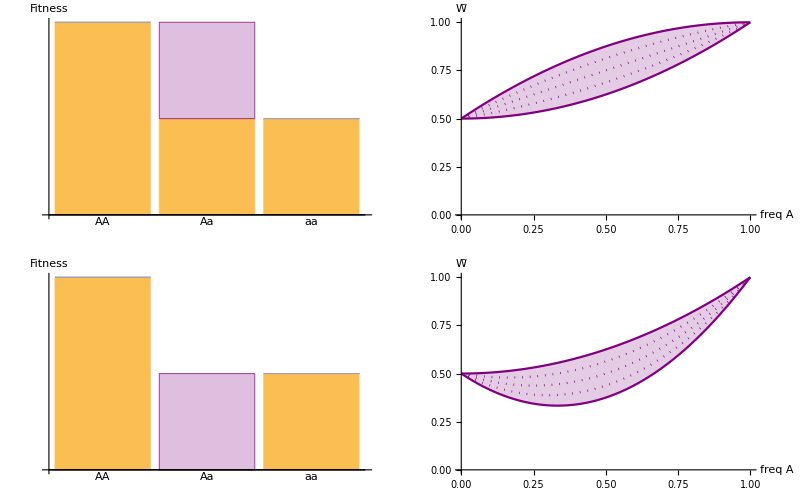

```mathematica
GraphicsGrid[
{{BarChart[{{1,0},{0.5,Style[0.5,{Purple,Opacity[0.25]}]},{0.5,0}},ChartLayout->"Stacked",Axes->{True,True},ChartLabels->{Placed[{"AA","Aa","aa"},Axis],None},AxesLabel->{"","Fitness"},Ticks->False],
Plot[{
p^2 1+2p(1-p)0.5+0.5(1-p)^2,
p^2 1+2p(1-p)0.625+0.5(1-p)^2,
p^2 1+2p(1-p)0.75+0.5(1-p)^2,
p^2 1+2p(1-p)0.875+0.5(1-p)^2,
p^2 1+2p(1-p)1+(1-p)^2*0.5},{p,0,1},AxesLabel->{"freq A","W̄"},Filling->{1->{5}},PlotStyle->{{Purple},{Purple,Dotted},{Purple,Dotted},{Purple,Dotted},{Purple}},Ticks->{True,False},PlotRange->{Automatic,{0,1}}]},
{BarChart[{{1,0},{0.0,Style[0.5,{Purple,Opacity[0.25]}]},{0.5,0}},ChartLayout->"Stacked",Axes->{True,True},ChartLabels->{Placed[{"AA","Aa","aa"},Axis],None},AxesLabel->{"","Fitness"},Ticks->False],
Plot[{
p^2 1+2p(1-p)0+0.5(1-p)^2,
p^2 1+2p(1-p)0.125+0.5(1-p)^2,
p^2 1+2p(1-p)0.25+0.5(1-p)^2,
p^2 1+2p(1-p)0.375+0.5(1-p)^2,
p^2 1+2p(1-p)0.5+(1-p)^2*0.5},{p,0,1},AxesLabel->{"freq A","W̄"},Filling->{1->{5}},PlotStyle->{{Purple},{Purple,Dotted},{Purple,Dotted},{Purple,Dotted},{Purple}},Ticks->{True,False},PlotRange->{Automatic,{0,1}}]}
}
]
```

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeDominantPayloadMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->0.5|>;
```

```mathematica
plot1=Plot3D[(1-p)^2 (1-q)^2+4 (1-p) p (1-q) q+2 p^2 (1-q) q+2 (1-p) p q^2+p^2 q^2,{p,0,1},{q,0,1},PlotRange->{Automatic,Automatic,{0,1}},AxesLabel->{"freq A","freq B","W̄"},BaseStyle->{FontSize->14},Ticks->{{0,1}, {0,1}},MeshStyle->{{Dashed}}]
```

-Graphics3D-

```mathematica
types=Genotypes/."Aw"->p/."Ad"->(1-p)/."Bw"->q/."Bd"->1-q;
```

```mathematica
geno=types[[;;,1,1]]*types[[;;,1,2]]*types[[;;,2,1]]*types[[;;,2,2]]
```

{p^2 q^2,p^2 (1-q) q,(1-p) p q^2,(1-p) p (1-q) q,p^2 (1-q) q,p^2 (1-q)^2,(1-p) p (1-q) q,(1-p) p (1-q)^2,(1-p) p q^2,(1-p) p (1-q) q,(1-p)^2 q^2,(1-p)^2 (1-q) q,(1-p) p (1-q) q,(1-p) p (1-q)^2,(1-p)^2 (1-q) q,(1-p)^2 (1-q)^2}

```mathematica
Fitness.geno/.ϵ->1/.s->0/.p->1-p/.q->1-q//Simplify
```

(-1+q)^2+p (-2+8 q-4 q^2)+p^2 (1-4 q+2 q^2)

```mathematica
Plot3D[1-q^2+p^2 (-1+2 q^2),{p,0,1},{q,0,1},PlotRange->{Automatic,Automatic,{0,1}}],{ϵ,0,1},{s,0,1}]
```

```mathematica
Manipulate[Plot3D[p q p q+2p q p (1-q)ϵ+2p q (1-p)q ϵ+2p q (1-p)(1-q)(1-s)+p(1-q)p(1-q)ϵ+2p(1-q)(1-p)q(1-s)+2p (1-q)(1-p)(1-q)(1-s)+(1-p)q (1-p)ϵ+2(1-p)q(1-p)(1-q)(1-s)+(1-p)(1-q)(1-p)(1-q),{p,0,1},{q,0,1}],{ϵ,0,1},{s,0,1}]
```

```mathematica
Plot3D[
p q p q+
2p q p (1-q)ϵ+
2p q (1-p)q ϵ+
2p q (1-p)(1-q)(1-s)+
p(1-q)p(1-q)ϵ+
2p(1-q)(1-p)q(1-s)+
2p (1-q)(1-p)(1-q)(1-s)+
(1-p)q (1-p)ϵ+
2(1-p)q(1-p)(1-q)(1-s)+
(1-p)(1-q)(1-p)(1-q)/.ϵ->0/.s->1,{p,0,1},{q,0,1},AxesLabel->{"Frequency a","Frequency b","W̄"}]
```

-Graphics3D-